```mathematica
(**Common Definitions**)
```

```mathematica
Q=1.82;Subscript[x, B]=0.34;M=0.938272;k=5.75;t=0.17;
```

```mathematica
(*Define β*)
```

```mathematica
β=(2 Subscript[x, B] M)/Sqrt[Q]
```

0.472936

```mathematica
(*Define y*)
```

```mathematica
y=Sqrt[Q]/(k β)
```

0.496096

```mathematica
(*Twist 3 Subscript[h, 3]^U=OverTilde[Subscript[h, 3]^U]*)
```

```mathematica
Subscript[h, 3U]:=(2 Subscript[x, B](y-2)Sqrt[(t(Subscript[x, B]-1)-M^2 Subscript[x, B]^2)(1-y)](β-1)Cos[ϕ*π/180])/((1+(β-1)Subscript[x, B])y^2)
```

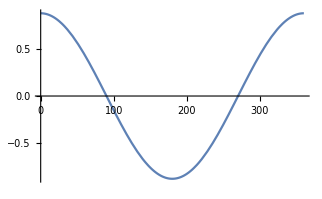

```mathematica
Plot[Im[Subscript[h, 3U]],{ϕ,0,360},PlotRange->Automatic]
```

```mathematica
(*Twist 4 Subscript[h, 4]^U=OverTilde[Subscript[h, 4]^U]*)
```

```mathematica
Subscript[h, 4U]:=1/(2(1+(β-1)Subscript[x, B])^2 y^2)*(8(β-1)^2 Subscript[x, B]^2(y-1)Cos[ϕ *π/180]^2(M^2 Subscript[x, B]^2-t Subscript[x, B]+t)-Subscript[x, B]^2(y-2)^2(M^2(2(β-1)Subscript[x, B]+1)^2+1)-2(β-1)^2 t(Subscript[x, B]-1))
```

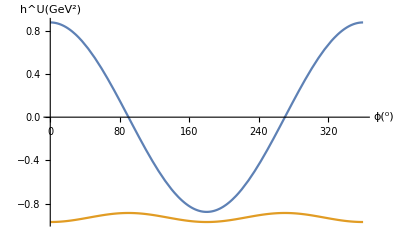

```mathematica
Plot[{Im[Subscript[h, 3U]],Subscript[h, 4U]},{ϕ,0,360},PlotRange->All,AxesLabel->{"ϕ(^0)","h^U(GeV^2)"}]
```